```mathematica
(* C3.AI COVID CHALLENGE *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
type = "Deaths_per_Million";
policy = "C6_Policy";
```

```mathematica
pD0 = 0.9122;
pD1=0.0748;
pD2 = 0;
pD3=0.0086;
pD4=0.0044;
pD0+pD1+pD2+pD3
```

0.9956

```mathematica
(* COnditional Prob *)
```

```mathematica
pD0C6l0=0.2874189425162114;
pD1C6l0=0.002604169114582501;
pD2C6l0 = 0.022727302272730225;
pD3C6l0=0.041666695833330415;
pD4C6l0= 1-pD0C6l0-pD1C6l0-pD2C6l0-pD3C6l0;
```

```mathematica
pD0C6l1=0.149878970024206;
pD1C6l1=0.002604169114582501;
pD2C6l1 = 0.022727302272730225;
pD3C6l1=0.041666695833330415;
pD4C6l1 = 1-pD0C6l1-pD1C6l1-pD2C6l1-pD3C6l1;
```

```mathematica
pD0C6l2=0;
pD1C6l2=0;
pD2C6l2 = 0;
pD3C6l2=0;
pD4C6l2 = 0;
```

```mathematica
pD0C6l3=0.4977749004450199;
pD1C6l3=0.15885394598965838;
pD2C6l3 = 0.022727302272730225;
pD3C6l3=0.8749999125000087;
pD4C6l3 = 1-pD0C6l3-pD1C6l3-pD2C6l3-pD3C6l3;
```

```mathematica
pD0C6l4=0.0649271870145626;
pD1C6l4=0.8359377157811767;
pD2C6l4 = 0.9318180931818093;
pD3C6l4=0.041666695833330415;
pD4C6l4 = 1-pD0C6l4-pD1C6l4-pD2C6l4-pD3C6l4;
```

```mathematica
(* C6 - 1 *)
```

```mathematica
prC6l0 = pD0 pD0C6l0 +  pD1 pD1C6l0+ pD2 pD2C6l0+ pD3 pD3C6l0+ pD4 pD4C6l0
```

0.265577

```mathematica
prC6l1= pD0 pD0C6l1 +  pD1 pD1C6l1+ pD2 pD2C6l1+ pD3 pD3C6l1+ pD4 pD4C6l1
```

0.140718

```mathematica
prC6l2= pD0 pD0C6l2 +  pD1 pD1C6l2+ pD2 pD2C6l2+ pD3 pD3C6l2+ pD4 pD4C6l2
```

0.

```mathematica
prC6l3= pD0 pD0C6l3 +  pD1 pD1C6l3+ pD2 pD2C6l3+ pD3 pD3C6l3+ pD4 pD4C6l3
```

0.471038

```mathematica
prC6l4= pD0 pD0C6l4 +  pD1 pD1C6l4+ pD2 pD2C6l4+ pD3 pD3C6l4+ pD4 pD4C6l4
```

0.118266

```mathematica
prC6l0+prC6l1+prC6l2+prC6l3+prC6l4
```

0.9956

```mathematica
(* Quantum Prob *)
```

```mathematica
interfC6l0 = Sqrt[pD0 pD0C6l0 pD1 pD1C6l0]Cos[θ00-θ10]+ Sqrt[pD0 pD0C6l0  pD2 pD2C6l0] Cos[θ00-θ20] +  Sqrt[pD0 pD0C6l0  pD3 pD3C6l0] Cos[θ00-θ30]+  Sqrt[ pD0 pD0C6l0  pD4 pD4C6l0] Cos[θ00-θ40]+
Sqrt[pD1 pD1C6l0  pD2 pD2C6l0 ] Cos[θ10-θ20]+ Sqrt[pD1 pD1C6l0  pD3 pD3C6l0] Cos[θ10-θ30]+Sqrt[pD1 pD1C6l0  pD4 pD4C6l0 ]Cos[θ10-θ40]+
Sqrt[pD2 pD2C6l0  pD3 pD3C6l0]  Cos[θ20-θ30]+ Sqrt[pD2 pD2C6l0  pD4 pD4C6l0 ]Cos[θ20-θ40]+Sqrt[pD3 pD3C6l0  pD4 pD4C6l0 ]Cos[θ30-θ40];
```

```mathematica
interfC6l1 = Sqrt[pD0 pD0C6l1 pD1 pD1C6l1]Cos[θ01-θ11]+ Sqrt[pD0 pD0C6l1 pD2 pD2C6l1] Cos[θ01-θ21] +  Sqrt[pD0 pD0C6l1  pD3 pD3C6l1] Cos[θ01-θ31]+ Sqrt[ pD0 pD0C6l1  pD4 pD4C6l1] Cos[θ01-θ41]+ 
Sqrt[pD1 pD1C6l1  pD2 pD2C6l1 ] Cos[θ11-θ21]+ Sqrt[pD1 pD1C6l1  pD3 pD3C6l1] Cos[θ11-θ31]+Sqrt[pD1 pD1C6l1 pD4 pD4C6l1] Cos[θ11-θ41]+
Sqrt[pD2 pD2C6l1  pD3 pD3C6l1 ] Cos[θ21-θ31]+ Sqrt[pD2 pD2C6l1  pD4 pD4C6l1] Cos[θ21-θ41]+Sqrt[pD3 pD3C6l1  pD4 pD4C6l1] Cos[θ31-θ41];
```

```mathematica
interfC6l2 = Sqrt[pD0 pD0C6l2 pD1 pD1C6l2]Cos[θ02-θ12]+ Sqrt[pD0 pD0C6l2 pD2 pD2C6l2] Cos[θ02-θ22] +  Sqrt[pD0 pD0C6l2  pD3 pD3C6l2] Cos[θ30-θ32]+ Sqrt[ pD0 pD0C6l2  pD4 pD4C6l2] Cos[θ02-θ42]+ 
Sqrt[pD1 pD1C6l2 pD2 pD2C6l2 ] Cos[θ12-θ22]+ Sqrt[pD1 pD1C6l2  pD3 pD3C6l2] Cos[θ12-θ32]+Sqrt[pD1 pD1C6l2 pD4 pD4C6l2] Cos[θ12-θ42]+
Sqrt[pD2 pD2C6l2  pD3 pD3C6l2 ] Cos[θ22-θ32]+ Sqrt[pD2 pD2C6l2  pD4 pD4C6l2] Cos[θ22-θ42]+Sqrt[pD3 pD3C6l2  pD4 pD4C6l2] Cos[θ32-θ42];
```

```mathematica
interfC6l3 = Sqrt[pD0 pD0C6l3 pD1 pD1C6l3]Cos[θ03-θ13]+ Sqrt[pD0 pD0C6l3 pD2 pD2C6l3] Cos[θ03-θ23] +  Sqrt[pD0 pD0C6l3  pD3 pD3C6l3] Cos[θ03-θ33]+ Sqrt[ pD0 pD0C6l3  pD4 pD4C6l3] Cos[θ03-θ43]+ 
Sqrt[pD1 pD1C6l3  pD2 pD2C6l3 ] Cos[θ13-θ23]+ Sqrt[pD1 pD1C6l3  pD3 pD3C6l3] Cos[θ13-θ33]+Sqrt[pD1 pD1C6l3 pD4 pD4C6l3] Cos[θ13-θ43]+
Sqrt[pD2 pD2C6l3  pD3 pD3C6l3 ] Cos[θ23-θ33]+ Sqrt[pD2 pD2C6l3  pD4 pD4C6l3] Cos[θ23-θ43]+Sqrt[pD3 pD3C6l3  pD4 pD4C6l3] Cos[θ33-θ43];
```

```mathematica
interfC6l4 = Sqrt[pD0 pD0C6l4 pD1 pD1C6l4]Cos[θ04-θ14]+ Sqrt[pD0 pD0C6l4 pD2 pD2C6l4] Cos[θ04-θ24] +  Sqrt[pD0 pD0C6l4  pD3 pD3C6l4] Cos[θ04-θ34]+ Sqrt[ pD0 pD0C6l4  pD4 pD4C6l4] Cos[θ04-θ44]+ 
Sqrt[pD1 pD1C6l4  pD2 pD2C6l4 ] Cos[θ14-θ24]+ Sqrt[pD1 pD1C6l4  pD3 pD3C6l4] Cos[θ14-θ34]+Sqrt[pD1 pD1C6l4 pD4 pD4C6l4] Cos[θ14-θ44]+
Sqrt[pD2 pD2C6l4  pD3 pD3C6l4 ] Cos[θ24-θ34]+ Sqrt[pD2 pD2C6l4  pD4 pD4C6l4] Cos[θ24-θ44]+Sqrt[pD3 pD3C6l4  pD4 pD4C6l4] Cos[θ34-θ44];
```

```mathematica
qprC6l0 = prC6l0 + 2 interfC6l0;
```

```mathematica
qprC6l1= prC6l1 + 2 interfC6l1;
```

```mathematica
qprC6l2= prC6l2 + 2 interfC6l2;
```

```mathematica
qprC6l3= prC6l3 + 2 interfC6l3;
```

```mathematica
qprC6l4= prC6l4 + 2 interfC6l4;
```

```mathematica
qprC6l0Norm = FullSimplify[qprC6l0/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)];
```

```mathematica
qprC6l1Norm = FullSimplify[qprC6l1/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)];
```

```mathematica
qprC6l2Norm = FullSimplify[qprC6l2/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)];
```

```mathematica
qprC6l3Norm = FullSimplify[qprC6l3/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)];
```

```mathematica
qprC6l4Norm =1- qprC6l3Norm-qprC6l2Norm-qprC6l1Norm-qprC6l0Norm;
```

```mathematica
Clear[θ00,θ10,θ20,θ30,θ40,
         θ01,θ11,θ21,θ31,θ41,
         θ02,θ12,θ22,θ32,θ42,
         θ03,θ13,θ23,θ33,θ43,
         θ04,θ14,θ24,θ34,θ44];
```

```mathematica
θ20=π;θ31=0.1;θ22=π/2;θ43=π/2;θ23=π;θ30=π;θ21=π;θ42=π;
```

```mathematica
res = FindInstance[{qprC6l0Norm+qprC6l1Norm+qprC6l2Norm +qprC6l3Norm+qprC6l4Norm== 1},{θ00,θ10,θ20,θ30,θ40,θ01,θ11,θ21,θ31,θ41,θ02,θ12,θ22,θ32,θ42,θ03,θ13,θ23,θ33,θ43, θ04,θ14,θ24,θ34,θ44}, Reals]
```

{{θ00→-12/5,θ10→-1/2,θ20→-9/5,θ30→3/5,θ40→-24/5,θ01→-21/5,θ11→11/5,θ21→-3/5,θ31→-6/5,θ41→-14/5,θ02→-19/5,θ12→-14/5,θ22→-41/10,θ32→-3/10,θ42→-17/10,θ03→18/5,θ13→-37/10,θ23→13/5,θ33→-39/10,θ43→-21/10,θ04→-22/5,θ14→1/10,θ24→1,θ34→-9/2,θ44→-33/10}}

```mathematica
(* Params *)
```

```mathematica
θ10=res[[1]][[2]][[2]];
θ20=res[[1]][[3]][[2]];
θ30=res[[1]][[4]][[2]];
θ40=res[[1]][[5]][[2]];
θ11=res[[1]][[7]][[2]];
θ21=res[[1]][[8]][[2]];
θ31=res[[1]][[9]][[2]];
θ41=res[[1]][[10]][[2]];
θ02=res[[1]][[11]][[2]];
θ12=res[[1]][[12]][[2]];
θ22=res[[1]][[13]][[2]];
θ32=res[[1]][[14]][[2]];
θ42=res[[1]][[15]][[2]];
θ03=res[[1]][[16]][[2]];
θ13=res[[1]][[17]][[2]];
θ23=res[[1]][[18]][[2]];
θ33=res[[1]][[19]][[2]];
θ43=res[[1]][[20]][[2]];
θ04=res[[1]][[16]][[2]];
θ14=res[[1]][[17]][[2]];
θ24=res[[1]][[18]][[2]];
θ34=res[[1]][[19]][[2]];
θ44=res[[1]][[20]][[2]];
```

```mathematica
(* Updated probabilities *)
```

```mathematica
qprC6l0Norm = Re[FullSimplify[qprC6l0/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)]]
```

Re[(13.7475+1.71873 Cos[θ00]+3.01589 Sin[θ00])/((62.3796+3.97501 ⅈ)+1.71873 Cos[θ00]-2.16157 Cos[θ01]+3.01589 Sin[θ00]-0.992725 Sin[θ01])]

```mathematica
qprC6l1Norm = Re[FullSimplify[qprC6l1/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)]]
```

Re[(13.6232-4.0599 Cos[θ01]-1.86455 Sin[θ01])/((117.162+7.46594 ⅈ)+3.22814 Cos[θ00]-4.0599 Cos[θ01]+5.66449 Sin[θ00]-1.86455 Sin[θ01])]

```mathematica
qprC6l2Norm = Re[FullSimplify[qprC6l2/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)]]
```

0.

```mathematica
qprC6l3Norm = Re[FullSimplify[qprC6l3/(qprC6l0+qprC6l1+qprC6l2 + qprC6l3+qprC6l4)]]
```

Re[(18.2296+1.59963 ⅈ)/((36.294+2.31276 ⅈ)+1. Cos[θ00]-1.25766 Cos[θ01]+1.75472 Sin[θ00]-0.577593 Sin[θ01])]

```mathematica
qprC6l4Norm =Re[1- qprC6l3Norm-qprC6l2Norm-qprC6l1Norm-qprC6l0Norm]
```

1.-Re[(13.6232-4.0599 Cos[θ01]-1.86455 Sin[θ01])/((117.162+7.46594 ⅈ)+3.22814 Cos[θ00]-4.0599 Cos[θ01]+5.66449 Sin[θ00]-1.86455 Sin[θ01])]-Re[(13.7475+1.71873 Cos[θ00]+3.01589 Sin[θ00])/((62.3796+3.97501 ⅈ)+1.71873 Cos[θ00]-2.16157 Cos[θ01]+3.01589 Sin[θ00]-0.992725 Sin[θ01])]-Re[(18.2296+1.59963 ⅈ)/((36.294+2.31276 ⅈ)+1. Cos[θ00]-1.25766 Cos[θ01]+1.75472 Sin[θ00]-0.577593 Sin[θ01])]

```mathematica
{qprC6l0Norm,qprC6l1Norm,qprC6l2Norm,qprC6l3Norm,qprC6l4Norm}
```

```mathematica
p0 = Plot3D[qprC6l0Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p1 = Plot3D[qprC6l1Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p2 = Plot3D[qprC6l2Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p3 = Plot3D[qprC6l3Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
p4 = Plot3D[qprC6l4Norm,{θ00,0,2π},{θ01,0,2π},ColorFunction->(ColorData["DarkRainbow"][#3]&),AxesLabel->{Style[type,16],Style[policy,16],Style["Prob",16]},BoundaryStyle->Thick, Boxed->False,Ticks->{{0,Pi/2,Pi,3Pi/2,2 Pi},{0,Pi/2,Pi,3Pi/2,2 Pi}, Automatic},TicksStyle->Directive[Black,12]];
```

```mathematica
Show[p0,p1]
```

-Graphics3D-

```mathematica
Show[p0,p3]
```

-Graphics3D-

```mathematica
Show[p0,p4]
```

-Graphics3D-

```mathematica
Show[p1,p3]
```

-Graphics3D-

```mathematica
Show[p1,p4]
```

-Graphics3D-

```mathematica
Show[p3,p4]
```

-Graphics3D-

```mathematica
fig=StreamDensityPlot[{qprC6l0Norm,qprC6l1Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

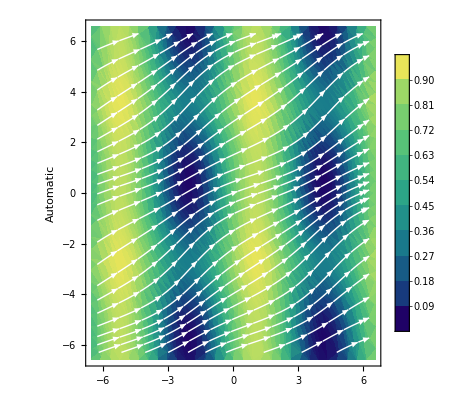

```mathematica
fig=StreamDensityPlot[{qprC6l0Norm,qprC6l3Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

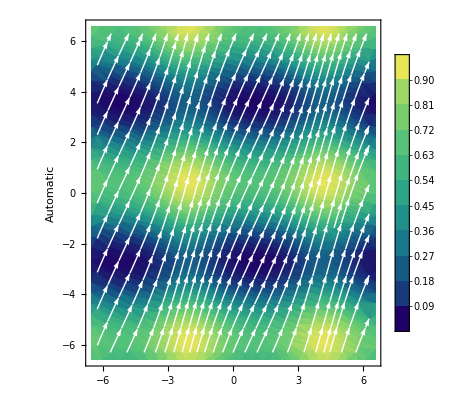

```mathematica
fig=StreamDensityPlot[{qprC6l0Norm,qprC6l4Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

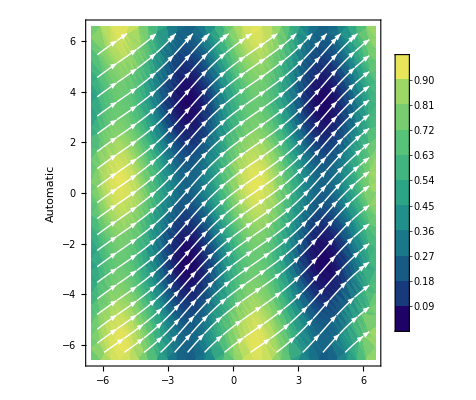

```mathematica
fig=StreamDensityPlot[{qprC6l1Norm,qprC6l3Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

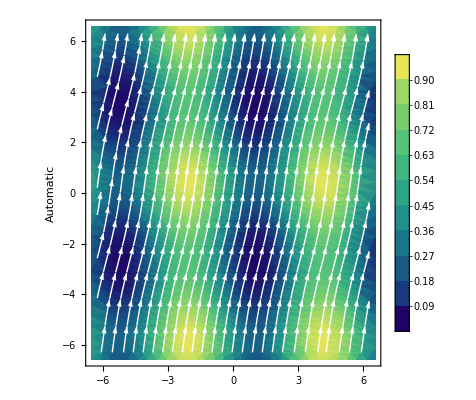

```mathematica
fig=StreamDensityPlot[{qprC6l1Norm,qprC6l4Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```

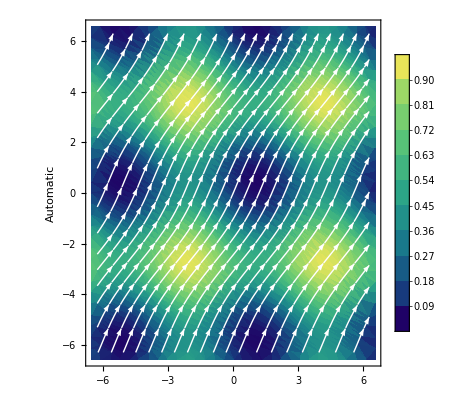

```mathematica
fig=StreamDensityPlot[{qprC6l3Norm,qprC6l4Norm},{θ00,-2π,2π},{θ01,-2π,2π},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[{"BlueGreenYellow",{0,1}},10],AxesLabel->Automatic,StreamStyle->{White, Thick}]
```